## from saved data

```mathematica
DumpGet["C:\\Users\\aliha\\Desktop\\optic flow\\sim1.mx"];
```

```mathematica
<<"C:\\Users\\aliha\\Desktop\\optic flow\\pyramidal-KLT.m";
<<"C:\\Users\\aliha\\Desktop\\optic flow\\VectorFieldOperations.m";
```

```mathematica
meanflow=meanFlowField[sim];
```

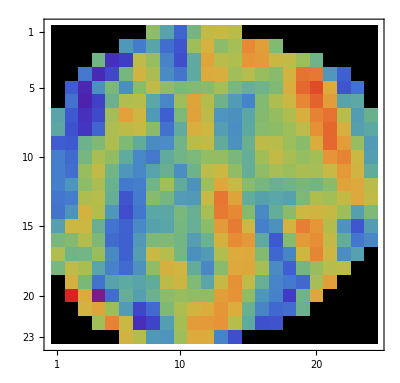
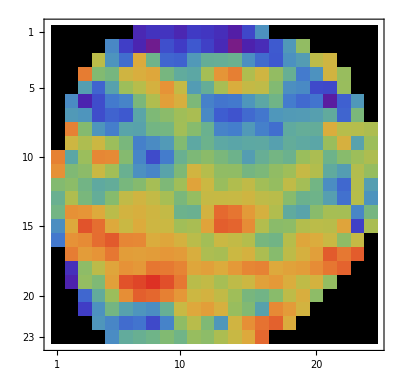
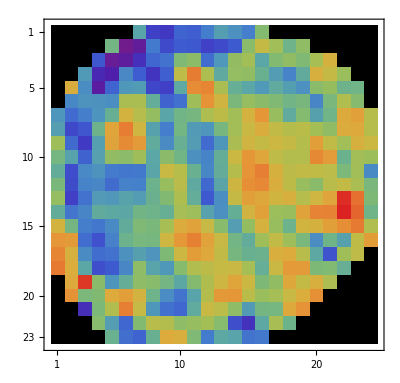
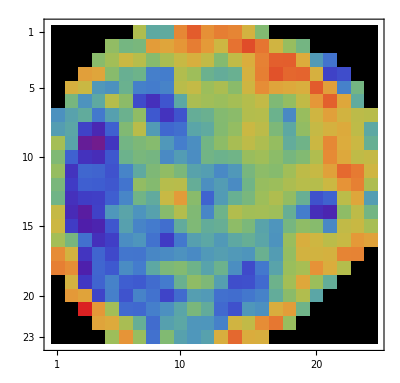
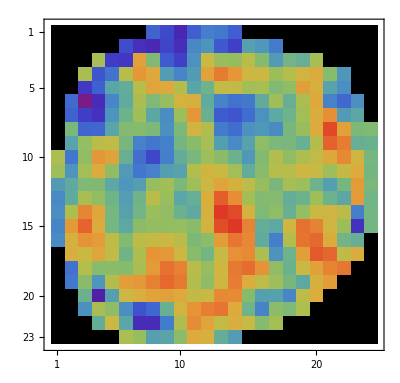
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{DVxx,DVyy,DVyx,DVxy,DVww,trace,array}=velocityGrad[OptionValue[KLTracker,"dgrid"],meanflow];
```

```mathematica
image=-Graphics-;
```

```mathematica
plotVectorField[meanflow,image]
```

-Graphics-

```mathematica
graphicsPrimitive=SRMeasures[DVxx,DVyy,DVxy,meanflow,array];
```

```mathematica
plotVectorFieldSR[graphicsPrimitive,meanflow,image,False]
```

```mathematica
plotVectorFieldSR[graphicsPrimitive,meanflow,image,True]
```

-Graphics-

## computing from start

```mathematica
(* imports *)
<<"C:\\Users\\aliha\\Desktop\\optic flow\\pyramidal-KLT.m";
<<"C:\\Users\\aliha\\Desktop\\optic flow\\VectorFieldOperations.m";

masks=Import["C:\\Users\\aliha\\Downloads\\Polarization_codes\\Polarization_codes\\time_binar.tif"][[;;160]];
imagedata=Import["C:\\Users\\aliha\\Downloads\\Polarization_codes\\Polarization_codes\\filtered.tif","Data"][[1;;160]];
images=Image[#,"Byte"]&/@imagedata;
imagedata=ImageData[#,Automatic]&/@images;
```

```mathematica
Options@KLTracker
```

{dgrid→8,threshold→0.99,windowFilter→30,pyramidNum→2,winSize→{20,20},maxIterations→{10,10},kthreshold→{0.05,0.05},blurRadius→1}

```mathematica
LaunchKernels[]
```

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
sim=KLTracker[images,imagedata,images,masks,1,Length[images],1]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

```mathematica
meanflow=meanFlowField[sim];
```

```mathematica
{DVxx,DVyy,DVxy,DVyx,DVww,trace,array}=velocityGrad[OptionValue[KLTracker,"dgrid"],meanflow];
```

```mathematica
plotVectorField[meanflow,images[[80]]]
```

-Graphics-

```mathematica
graphicsPrimitive=SRMeasures[DVxx,DVyy,DVxy,meanflow,array];
```

```mathematica
plotVectorFieldSR[graphicsPrimitive,meanflow,images[[80]],True]
```